Defining det as in Eq. 3

```mathematica
airyDeterminant[α_,β_]:=AiryAi[-α]AiryBi[β-α]-AiryAi[β-α]AiryBi[-α]
```

Creating Figure 1

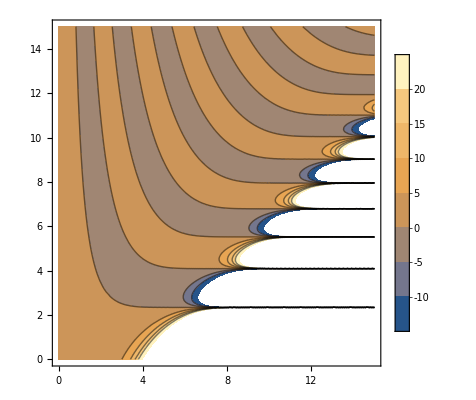

```mathematica
ContourPlot[airyDeterminant[α,β],{β,0,15},{α,0,15},PlotPoints->20,PlotLegends->True]
```

Here we numerically solve det(α,10) = 0.  We first plot it to find the approximate locations of the roots.  Then we instruct Mathematica to find roots near these approximate locations to far greater precision.  These roots assist us in finding and plotting the eigenstates.

Finding approximate locations of the roots, visually:

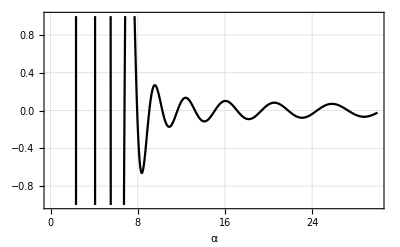

```mathematica
Plot[airyDeterminant[α,β]/.β->10,{α,0,30},PlotStyle->{Black},Frame->True,PlotRange->{{0,30},{-1,1}},GridLines->Automatic,AxesLabel->{α,None}]
```

Numerically solving for these roots to higher precision:

```mathematica
somealpha=Table[
α/.FindRoot[airyDeterminant[α,10],{α,n}],
{n,{2,4,5.5,6.8,7.5,9,10,11.5,13}}]
```

{2.33811,4.08795,5.52056,6.78679,7.94738,9.06461,10.2611,11.6484,13.2562}

With these roots, showing the eigenstates graphically:

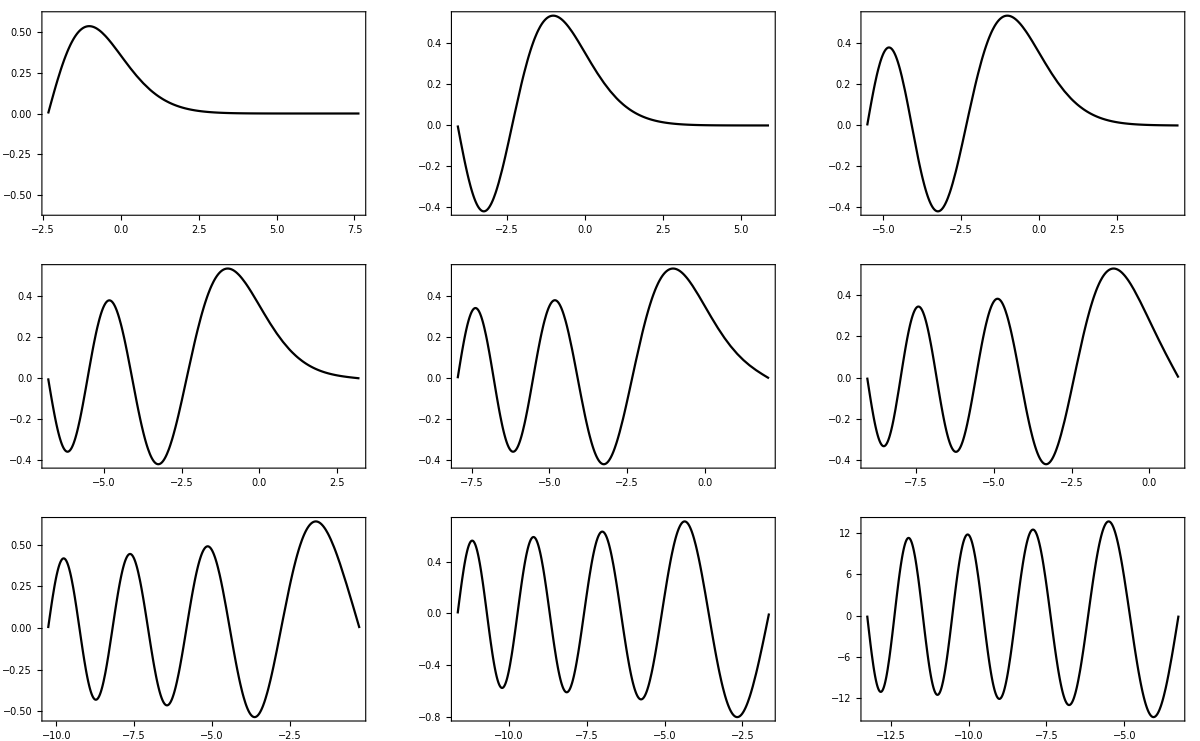

```mathematica
GraphicsGrid[ArrayReshape[{Plot[AiryAi[y]-AiryAi[-α]/AiryBi[-α] AiryBi[y]/.α->somealpha[[1]],
{y,-somealpha[[1]],10-somealpha[[1]]},
Frame->True,PlotRange->{Automatic,{-0.6,0.6}},PlotStyle->Black,Axes->False,FrameTicks->None],Table[Plot[AiryAi[y]-AiryAi[-α]/AiryBi[-α] AiryBi[y]/.α->somealpha[[n]],
{y,-somealpha[[n]],10-somealpha[[n]]},
Frame->True,PlotStyle->Black,Axes->False,FrameTicks->None],
{n,2,9}]},{3,3}],Frame->True]
```

Here, we numerically determine the (α,β) that will make E = FL.

```mathematica
FindRoot[{airyDeterminant[α,β],α-β},{{α,2},{β,2}}]
```

{α→2.66635,β→2.66635}

Comparison to WKB Approximation
Here, we compare the exact eigenvalues to those calculated with the WKB approximation (or the approximation at low L or high E).  We calculate for β = 1, a smaller value of β that yields a close match.

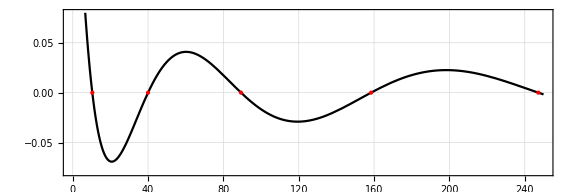

```mathematica
wkbeig=Table[α/.FindRoot[α^(3/2)-(α-1)^(3/2)-(3 Pi n)/2,{α,100}],{n,1,5}];
Plot[airyDeterminant[α,1],{α,0,250},PlotStyle->Black,PlotRange->{{0,250},{-0.08,0.08}},GridLines->Automatic,Frame->True,AspectRatio->1/3,ImageSize->Large,Epilog->{Red,PointSize@Medium,Table[Point[{α,0}],{α,wkbeig}]}]
```

The approximation at the lower eigenvalues begins to deteriorate at higher β.  The approximation is incapable of determining eigenvalues where α < β since the approximation is invalid for these cases.  Here, β = 10

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

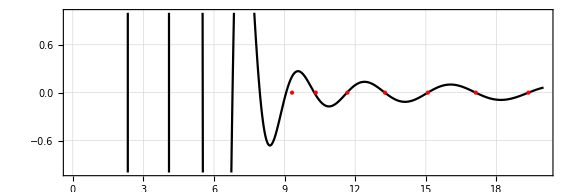

```mathematica
wkbeig=Table[α/.FindRoot[α^(3/2)-(α-10)^(3/2)-(3 Pi n)/2,{α,100}],{n,6,12}];
Plot[airyDeterminant[α,10],{α,0,20},PlotStyle->Black,PlotRange->{{0,20},{-1,1}},GridLines->Automatic,Frame->True,AspectRatio->1/3,ImageSize->Large,Epilog->{Red,PointSize@Medium,Table[Point[{α,0}],{α,wkbeig}]}]
```